1000

| Estimate | Standard Error | t-Statistic | P-Value
Ref | 2.25017 | 0.0124798 | 180.304 | 4.18801×10^-39
mue | 25.0323 | 0.0110989 | 2255.39 | 1.96108×10^-65

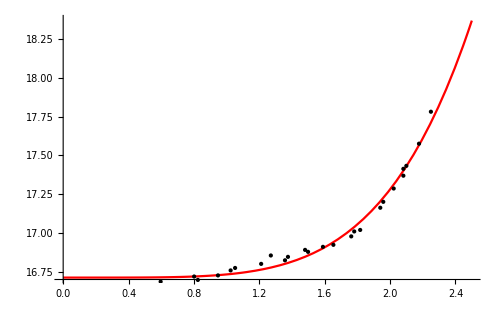

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["noyola.dat"];
L=Length[data];
Ie=1000
(*Ref = 12*)
M[R_]:=10^(8.32678*0.25*Log[R]-8.32678*0.25*Log[Ref])+mue-8.32
(*Plot[Log[Ip[R]],{R,0,12}]*)
fit = NonlinearModelFit[data,M[R],{Ref,mue},R,MaxIterations->1000];
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,0,2.5},PlotStyle->Red,Epilog:>Point[data],ImageSize->500]
```